```mathematica
nbdir=ToString[NotebookDirectory[]]
```

/home/mls/Code/multimode/

```mathematica
dir1=nbdir<>"fP=100_Delta0=50_N=1000_zA=0_epsilon=0_E0=50_96-grid_K-kerns_grid-factor";
SetDirectory[dir1]
filename=FileNames["*h5"][[1]];
t1 = Import[filename, {"Datasets", "/1/t"}];
x1 = Import[filename, {"Datasets", "/1/x"}];
y1 = Import[filename, {"Datasets", "/1/y"}];
imatom1 = Import[filename, {"Datasets", "/1/imatom"}];
reatom1 = Import[filename, {"Datasets", "/1/reatom"}];
imlight1 = Import[filename, {"Datasets", "/1/imlight"}];
relight1 = Import[filename, {"Datasets", "/1/relight"}];
modatomsq1 = Import[filename, {"Datasets", "/1/modatom"}];
modlightsq1= Import[filename, {"Datasets", "/1/modlight"}];
relightint1 = Import[filename, {"Datasets", "/1/relightint"}];
imlightint1 = Import[filename, {"Datasets", "/1/imlightint"}];
ResetDirectory[];
```

/home/mls/Code/multimode/fP=100_Delta0=50_N=1000_zA=0_epsilon=0_E0=50_96-grid_K-kerns_grid-factor

```mathematica
dir2=nbdir<>"fP=100_Delta0=-50_N=1000_zA=0_epsilon=0_E0=50_96-grid_K-kerns_grid-factor";
SetDirectory[dir2]
filename=FileNames["*h5"][[1]];
t2 = Import[filename, {"Datasets", "/1/t"}];
x2 = Import[filename, {"Datasets", "/1/x"}];
y2 = Import[filename, {"Datasets", "/1/y"}];
imatom2 = Import[filename, {"Datasets", "/1/imatom"}];
reatom2 = Import[filename, {"Datasets", "/1/reatom"}];
imlight2 = Import[filename, {"Datasets", "/1/imlight"}];
relight2 = Import[filename, {"Datasets", "/1/relight"}];
modatomsq2 = Import[filename, {"Datasets", "/1/modatom"}];
modlightsq2= Import[filename, {"Datasets", "/1/modlight"}];
relightint2 = Import[filename, {"Datasets", "/1/relightint"}];
imlightint2 = Import[filename, {"Datasets", "/1/imlightint"}];
ResetDirectory[];
```

/home/mls/Code/multimode/fP=100_Delta0=-50_N=1000_zA=0_epsilon=0_E0=50_96-grid_K-kerns_grid-factor

```mathematica
(* Declare variables, max variables *)
```

```mathematica
tmax=Length[t1]
ymax1=Length[y1];
xmax1=Length[x1]
xmid1=xmax1/2+1;
{First[x1], Last[x1]}
```

501

96

{-12.,11.75}

```mathematica
tmax2=Length[t2]
ymax2=Length[y2];
xmax2=Length[x2]
xmid2=xmax2/2+1;
{First[x2], Last[x2]}
```

501

96

{-12.,11.75}

```mathematica
(* Abs atomic field density plot *)
```

```mathematica
tmax==tmax2
```

True

```mathematica
plotmax=tmax;
plotint=20;
```

## 1D plots

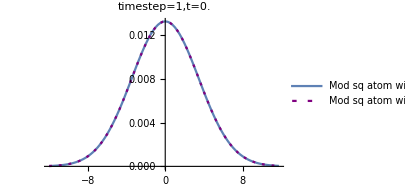
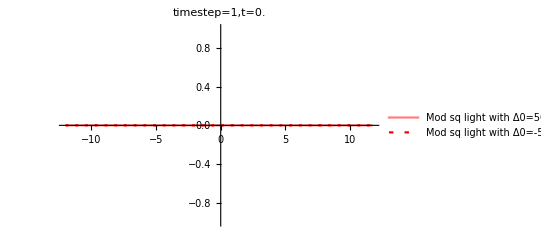
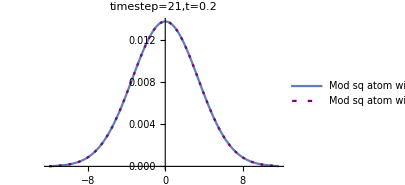
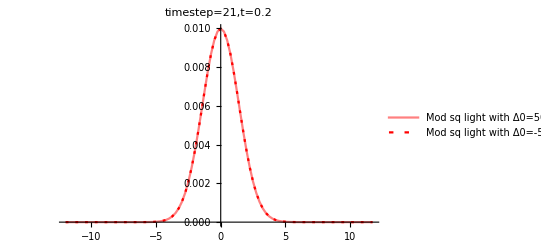
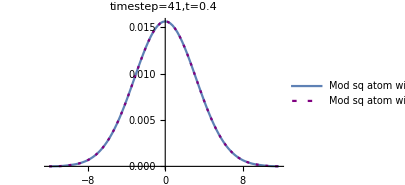
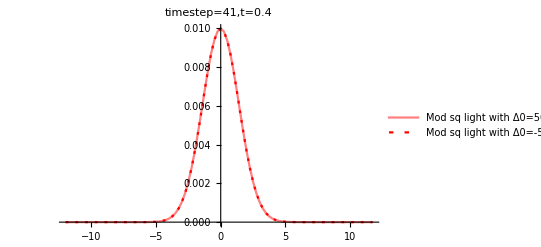
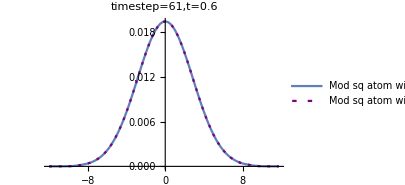
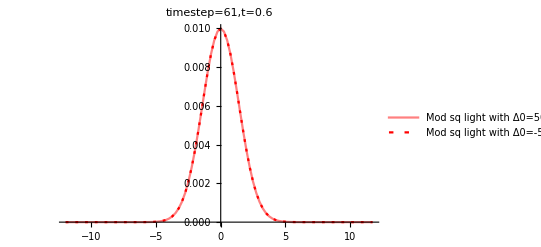

```mathematica
(* Abs val of atomic and light field by time step *)
Table[{ListLinePlot[{Table[{ x1[[i]] ,modatomsq1[[t,i,xmid1]]} ,{i,1,xmax1}],Table[{ x2[[i]] ,modatomsq2[[t,i,xmid2]]} ,{i,1,xmax2}]},ImageSize->300,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotLegends->Placed[{"Mod sq atom with Δ0=50","Mod sq atom with Δ0=-50"},Below],PlotStyle->{Thick,{Purple,Thick,AbsoluteDashing[{2,5}]}},PlotRange->All],ListLinePlot[{Table[{ x1[[i]],modlightsq1[[t,i,xmid1]]} ,{i,1,xmax1}],Table[{ x2[[i]],modlightsq2[[ t,i,xmid2]]} ,{i,1,xmax2}]},ImageSize->400,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotStyle->{{Pink,Thick},{Red,Thick,AbsoluteDashing[{2,5}]}},PlotLegends->Placed[{"Mod sq light with Δ0=50","Mod sq light with Δ0=-50"},Below],PlotRange->All]},{t,1,plotmax,plotint}]
```

```mathematica
(* Real part of atomic and light field by time step *)
```

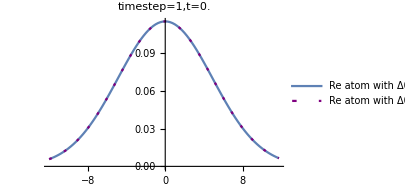
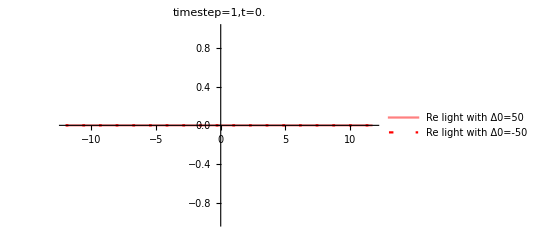
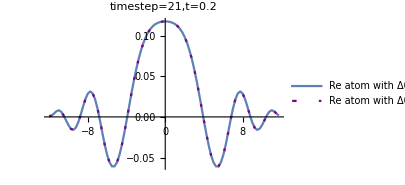
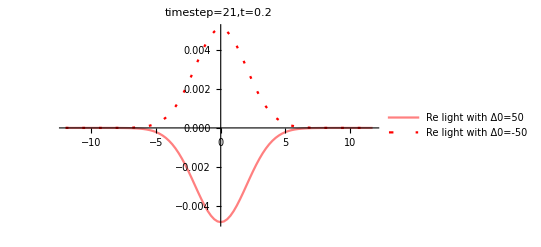
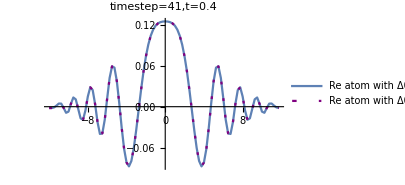
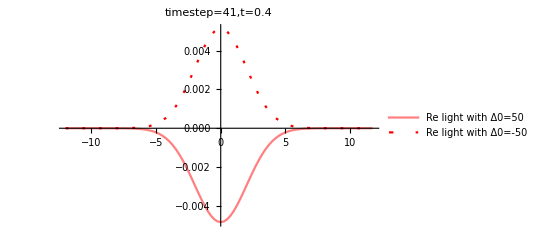
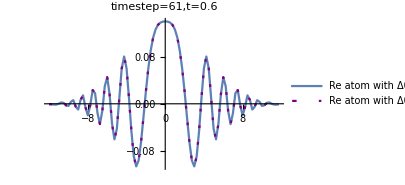
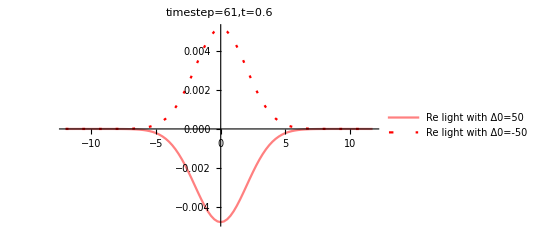

```mathematica
Table[{ListLinePlot[{Table[{ x1[[i]] ,reatom1[[t,i,xmid1]]} ,{i,1,xmax1}],Table[{ x2[[i]] ,reatom2[[t,i,xmid2]]} ,{i,1,xmax2}]},ImageSize->300,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotLegends->Placed[{"Re atom with Δ0=50","Re atom with Δ0=-50"},Below],PlotStyle->{Thick,{Purple,Thick,AbsoluteDashing[{2,10}]}},PlotRange->All],ListLinePlot[{Table[{ x1[[i]],relight1[[t,i,xmid1]]} ,{i,1,xmax1}],Table[{ x2[[i]],relight2[[t,i,xmid2]]} ,{i,1,xmax2}]},ImageSize->400,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotStyle->{{Pink,Thick},{Red,Thick,AbsoluteDashing[{2,10}]}},PlotLegends->Placed[{"Re light with Δ0=50","Re light with Δ0=-50"},Below],PlotRange->All]},{t,1,plotmax,plotint}]
```

```mathematica
(* Im part of atomic and light field by time step *)
```

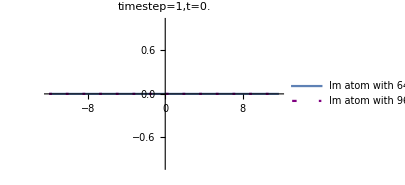
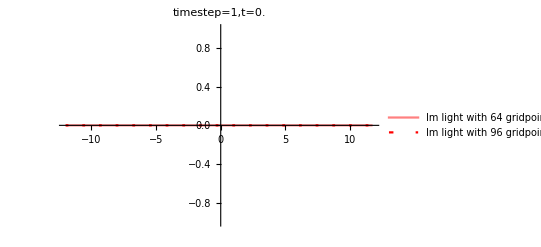
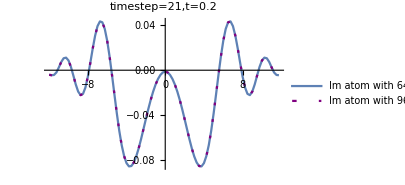
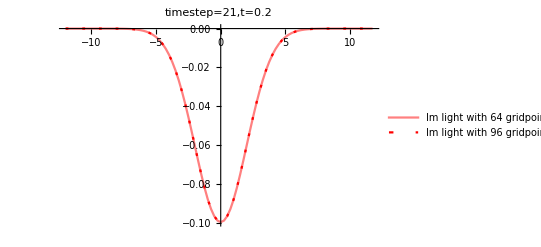
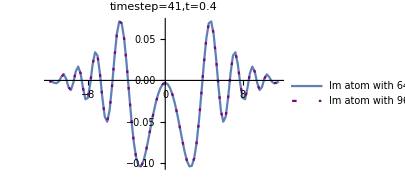
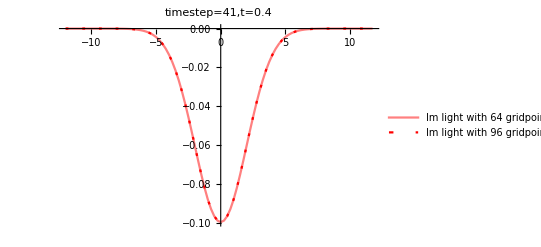
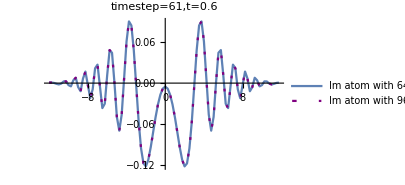
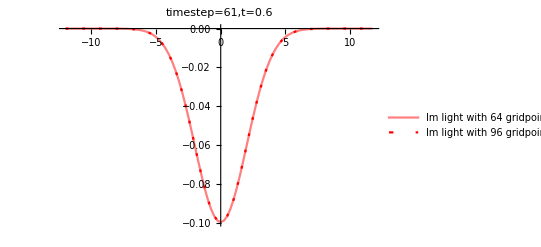
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Table[{ListLinePlot[{Table[{ x1[[i]] ,imatom1[[t,i,xmid1]]} ,{i,1,xmax1}],Table[{ x2[[i]] ,imatom2[[t,i,xmid2]]} ,{i,1,xmax2}]},ImageSize->300,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotLegends->Placed[{"Im atom with 64 gridpoints","Im atom with 96 gridpoints"},Below],PlotStyle->{Thick,{Purple,Thick,AbsoluteDashing[{2,10}]}},PlotRange->All],ListLinePlot[{Table[{ x1[[i]],imlight1[[t,i,xmid1]]} ,{i,1,xmax1}],Table[{ x2[[i]],imlight2[[t,i,xmid2]]} ,{i,1,xmax2}]},ImageSize->400,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotStyle->{{Pink,Thick},{Red,Thick,AbsoluteDashing[{2,10}]}},PlotLegends->Placed[{"Im light with 64 gridpoints","Im light with 96 gridpoints"},Below],PlotRange->All]},{t,1,plotmax,plotint}]
```

```mathematica
(* Light int by time step *)
```

```mathematica
Table[{ListLinePlot[{Table[{ x1[[i]] ,relightint1[[t,i,xmid1]]} ,{i,1,xmax1}],Table[{ x2[[i]] ,relightint2[[t,i,xmid2]]} ,{i,1,xmax2}],Table[{ x3[[i]] ,relightint3[[t,i,xmid3]]} ,{i,1,xmax3}]},ImageSize->300,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotLegends->Placed[{"Im atom with 64 gridpoints","Im atom with 96 gridpoints","Im light with 128 gridpoints"},Below],PlotStyle->{Thick,{Purple,Thick,AbsoluteDashing[{2,5}]},{Green,Thick,AbsoluteDashing[{2,10}]}},PlotRange->All],ListLinePlot[{Table[{ x1[[i]],imlightint1[[t,i,xmid1]]} ,{i,1,xmax1}],Table[{ x2[[i]],imlightint2[[t,i,xmid2]]} ,{i,1,xmax2}],Table[{ x3[[i]] ,imlightint3[[t,i,xmid3]]} ,{i,1,xmax3}]},ImageSize->400,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotStyle->{{Pink,Thick},{Red,Thick,AbsoluteDashing[{2,5}]},{Purple,Thick,AbsoluteDashing[{2,10}]}},PlotLegends->Placed[{"Im light with 64 gridpoints","Im light with 96 gridpoints","Im light with 128 gridpoints"},Below],PlotRange->All]},{t,1,plotmax,plotint}]
```

Table::iterb: Iterator {i,1,xmax3} does not have appropriate bounds.

Table::iterb: Iterator {i,1.,xmax3} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListLinePlot::lpn: {{{-12.,0.},{-11.75,0.},{-11.5,0.},{-11.25,0.},{-11.,0.},{-10.75,0.},{-10.5,0.},{-10.25,0.},{-10.,0.},{-9.75,0.},«32»,{-1.5,0.},{-1.25,0.},{-1.,0.},{-0.75,0.},{-0.5,0.},{-0.25,0.},{0.,0.},{0.25,0.},«46»},{«1»},«1»} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

{{ListLinePlot[1],ListLinePlot[{{{-12.,0.},{-11.75,0.},{-11.5,0.},{-11.25,0.},{-11.,0.},{-10.75,0.},{-10.5,0.},83,{10.5,0.},{10.75,0.},{11.,0.},{11.25,0.},{11.5,0.},{11.75,0.}},{1},1},4,1]},25}
 |  |  |  |

## 2D graphs

```mathematica
(*Table[{ListDensityPlot[Flatten[Table[{ x1[[i]] ,y1[[j]],modatomsq1[[t,i,j]]} ,{i,1,xmax1},{j,1,ymax1}],1],ImageSize->300,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotRange->All],ListDensityPlot[Flatten[Table[{ x2[[i]] ,y2[[j]],modatomsq2[[t,i,j]]} ,{i,1,xmax2},{j,1,ymax2}],1],ImageSize->300,PlotLabel->StringForm["timestep=`1`,t=`2`",t,t1[[t]]],PlotRange->All,ColorFunction->"BlueGreenYellow"]},{t,1,plotmax,plotint}]*)
```